# Hill Equation Parameters adj

## Solutions to Hill equation

```mathematica
Solve[1+v-u*(1+v)+a==0&&1+u^-1-v*(1+u^-1)+b==0,{u,v}]
```

## Assign solutions to u & v

```mathematica
(*f[u_,v_]:={1-u+a*1/(1+v),100-v+b*1/(1+u^-1)}fu和gv永远同时为负，无法出现Turing Pattern*)
f[u_,v_]:={1+v-u*(1+v)+a,1+u^-1-v*(1+u^-1)+b}(*变式同样*)
equations=Thread[f[u,v]==0]
solution=Solve[equations,{u,v}]
(*solution=Solve[1-u+a*1/(1+v)==0&&1-10v+b*1/(1+u^-1)==0,{u,v}]*)
{u1,v1}={u,v}/. solution[[2]]
{u2,v2}={u,v}/. solution[[1]]
```

{1+a+v-u (1+v)==0,1+b+1/u-(1+1/u) v==0}

{{u→(a+b-√(16+8 a+a^2+8 b+6 a b+b^2))/(2 (2+b)),v→1/2 (-a+a/(2+b)+b/(2+b)+(a b)/(2 (2+b))+b^2/(2 (2+b))-(√(16+8 a+a^2+8 b+6 a b+b^2))/(2+b)-(b √(16+8 a+a^2+8 b+6 a b+b^2))/(2 (2+b)))},{u→(a+b+√(16+8 a+a^2+8 b+6 a b+b^2))/(2 (2+b)),v→1/2 (-a+a/(2+b)+b/(2+b)+(a b)/(2 (2+b))+b^2/(2 (2+b))+(√(16+8 a+a^2+8 b+6 a b+b^2))/(2+b)+(b √(16+8 a+a^2+8 b+6 a b+b^2))/(2 (2+b)))}}

{(a+b+√(16+8 a+a^2+8 b+6 a b+b^2))/(2 (2+b)),1/2 (-a+a/(2+b)+b/(2+b)+(a b)/(2 (2+b))+b^2/(2 (2+b))+(√(16+8 a+a^2+8 b+6 a b+b^2))/(2+b)+(b √(16+8 a+a^2+8 b+6 a b+b^2))/(2 (2+b)))}

{(a+b-√(16+8 a+a^2+8 b+6 a b+b^2))/(2 (2+b)),1/2 (-a+a/(2+b)+b/(2+b)+(a b)/(2 (2+b))+b^2/(2 (2+b))-(√(16+8 a+a^2+8 b+6 a b+b^2))/(2+b)-(b √(16+8 a+a^2+8 b+6 a b+b^2))/(2 (2+b)))}

## Solution 1 (2nd one):

```mathematica
test1=f[u1,v1]
test2=f[u2,v2]

check1=Simplify[test1=={0,0}]
check2=Simplify[test2=={0,0}]
```

{1+a+1/2 (-a+a/(2+b)+b/(2+b)+(a b)/(2 (2+b))+b^2/(2 (2+b))+(√(16+8 a+a^2+8 b+6 a b+b^2))/(2+b)+(b √(16+8 a+a^2+8 b+6 a b+b^2))/(2 (2+b)))-((a+b+√(16+8 a+a^2+8 b+6 a b+b^2)) (1+1/2 (-a+a/(2+b)+b/(2+b)+(a b)/(2 (2+b))+b^2/(2 (2+b))+(√(16+8 a+a^2+8 b+6 a b+b^2))/(2+b)+(b √(16+8 a+a^2+8 b+6 a b+b^2))/(2 (2+b)))))/(2 (2+b)),1+b+(2 (2+b))/(a+b+√(16+8 a+a^2+8 b+6 a b+b^2))-1/2 (-a+a/(2+b)+b/(2+b)+(a b)/(2 (2+b))+b^2/(2 (2+b))+(√(16+8 a+a^2+8 b+6 a b+b^2))/(2+b)+(b √(16+8 a+a^2+8 b+6 a b+b^2))/(2 (2+b))) (1+(2 (2+b))/(a+b+√(16+8 a+a^2+8 b+6 a b+b^2)))}

{1+a+1/2 (-a+a/(2+b)+b/(2+b)+(a b)/(2 (2+b))+b^2/(2 (2+b))-(√(16+8 a+a^2+8 b+6 a b+b^2))/(2+b)-(b √(16+8 a+a^2+8 b+6 a b+b^2))/(2 (2+b)))-((a+b-√(16+8 a+a^2+8 b+6 a b+b^2)) (1+1/2 (-a+a/(2+b)+b/(2+b)+(a b)/(2 (2+b))+b^2/(2 (2+b))-(√(16+8 a+a^2+8 b+6 a b+b^2))/(2+b)-(b √(16+8 a+a^2+8 b+6 a b+b^2))/(2 (2+b)))))/(2 (2+b)),1+b+(2 (2+b))/(a+b-√(16+8 a+a^2+8 b+6 a b+b^2))-1/2 (-a+a/(2+b)+b/(2+b)+(a b)/(2 (2+b))+b^2/(2 (2+b))-(√(16+8 a+a^2+8 b+6 a b+b^2))/(2+b)-(b √(16+8 a+a^2+8 b+6 a b+b^2))/(2 (2+b))) (1+(2 (2+b))/(a+b-√(16+8 a+a^2+8 b+6 a b+b^2)))}

True

True

## Construct Jacobian Matrix

{(a+b+√(16+8 a+a^2+8 b+6 a b+b^2))/(2 (2+b)),1/2 (-a+a/(2+b)+b/(2+b)+(a b)/(2 (2+b))+b^2/(2 (2+b))+(√(16+8 a+a^2+8 b+6 a b+b^2))/(2+b)+(b √(16+8 a+a^2+8 b+6 a b+b^2))/(2 (2+b)))}

(1/4 (-4+a-b-√(a^2+(4+b)^2+a (8+6 b))) | 1-(a+b+√(a^2+(4+b)^2+a (8+6 b)))/(2 (2+b))
((2+b)^2 (-4-a+b+√(a^2+(4+b)^2+a (8+6 b))))/((a+b+√(a^2+(4+b)^2+a (8+6 b)))^2) | -1-(2 (2+b))/(a+b+√(a^2+(4+b)^2+a (8+6 b))))

1/4 (-4+a-b-√(a^2+(4+b)^2+a (8+6 b)))

1-(a+b+√(a^2+(4+b)^2+a (8+6 b)))/(2 (2+b))

((2+b)^2 (-4-a+b+√(a^2+(4+b)^2+a (8+6 b))))/((a+b+√(a^2+(4+b)^2+a (8+6 b)))^2)

-1-(2 (2+b))/(a+b+√(a^2+(4+b)^2+a (8+6 b)))

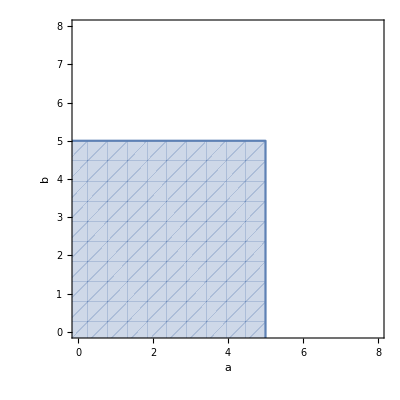

```mathematica
(*f[u_,v_]:={1-u+a*1/(1+v),1-10v+b*1/(1+u^-1)}*)
point={u1,v1}
jacobian1=D[f[u,v],{{u,v}}]/. {u->point[[1]],v->point[[2]]};
simplifiedJacobian1=Simplify[jacobian1];
MatrixForm[simplifiedJacobian1]

(*assign value*)
fu1=simplifiedJacobian1[[1,1]]
fv1=simplifiedJacobian1[[1,2]]
gu1=simplifiedJacobian1[[2,1]]
gv1=simplifiedJacobian1[[2,2]]

(*Condition 1.fu+gv<0 &&2.fu*gv-fv*gu>0*)
RegionPlot[fu1+gv1<0&&fu1*gv1-fv1*gu1>0,{a,-5,5},{b,-5,5},FrameLabel->{"a","b"},LabelStyle->Directive[Black,Medium],PlotRange->{{0,8},{0,8}}]
```

1

2

1.0098

101.005

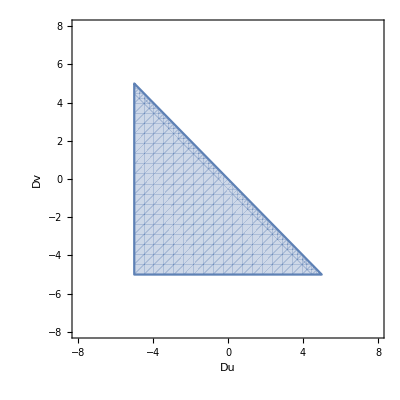

1+1357952/((203+√42033)^2 (209+√42033)^2)

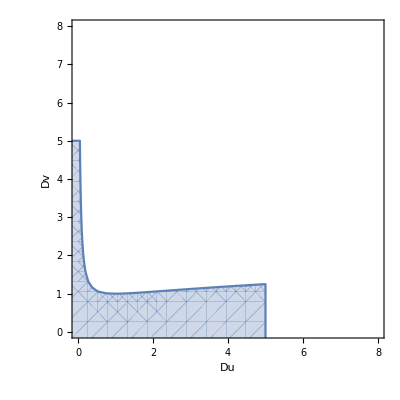

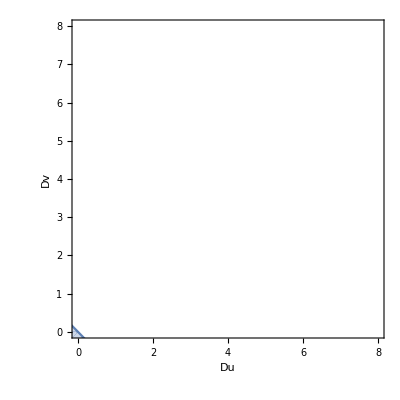

```mathematica
a=1
b=2
(*Steady States' numeric value*)
u1_v=N[u1]
v1_v=N[v1]
(*Condition 3.Du*gv+Dv*fu>0*)
plot1 =RegionPlot[Du*gv1+Dv*fu1>0,{Du,-5,5},{Dv,-5,5},FrameLabel->{"Du","Dv"},LabelStyle->Directive[Black,Medium],PlotRange->{{-8,8},{-8,8}}]
det1=fu1*gv1-fv1*gu1
(*Condition 4.(fu/Du+gv/Dv)^2>4*det/DuDv*)
plot2 =RegionPlot[(fu1/Du+gv1/Dv)^2>4*det1/Du*Dv,{Du,-5,5},{Dv,-5,5},FrameLabel->{"Du","Dv"},LabelStyle->Directive[Black,Medium],PlotRange->{{0,8},{0,8}}]

(*Condition 3&&4 *)
plot3 =RegionPlot[(fu1/Du+gv1/Dv)^2>4*det1/Du*Dv&&Du*gv1+Dv*fu1>0,{Du,-5,5},{Dv,-5,5},FrameLabel->{"Du","Dv"},LabelStyle->Directive[Black,Medium],PlotRange->{{0,8},{0,8}}]
```

## Solution 2 (1st one):

```mathematica
f[u_,v_]:={1-u+a*1/(1+v),1-v+b*1/(1+u^-1)}
equations=Thread[f[u,v]==0]
solution=Solve[equations,{u,v}]
(*solution=Solve[1-u+a*1/(1+v)==0&&1-10v+b*1/(1+u^-1)==0,{u,v}]*)
{u1,v1}={u,v}/. solution[[2]]
{u2,v2}={u,v}/. solution[[1]]
```

{1-u+a/(1+v)==0,1+b/(1+1/u)-v==0}

{{u→(a+b-√(16+8 a+a^2+8 b+6 a b+b^2))/(2 (2+b)),v→1/2 (-a+a/(2+b)+b/(2+b)+(a b)/(2 (2+b))+b^2/(2 (2+b))-(√(16+8 a+a^2+8 b+6 a b+b^2))/(2+b)-(b √(16+8 a+a^2+8 b+6 a b+b^2))/(2 (2+b)))},{u→(a+b+√(16+8 a+a^2+8 b+6 a b+b^2))/(2 (2+b)),v→1/2 (-a+a/(2+b)+b/(2+b)+(a b)/(2 (2+b))+b^2/(2 (2+b))+(√(16+8 a+a^2+8 b+6 a b+b^2))/(2+b)+(b √(16+8 a+a^2+8 b+6 a b+b^2))/(2 (2+b)))}}

{(a+b+√(16+8 a+a^2+8 b+6 a b+b^2))/(2 (2+b)),1/2 (-a+a/(2+b)+b/(2+b)+(a b)/(2 (2+b))+b^2/(2 (2+b))+(√(16+8 a+a^2+8 b+6 a b+b^2))/(2+b)+(b √(16+8 a+a^2+8 b+6 a b+b^2))/(2 (2+b)))}

{(a+b-√(16+8 a+a^2+8 b+6 a b+b^2))/(2 (2+b)),1/2 (-a+a/(2+b)+b/(2+b)+(a b)/(2 (2+b))+b^2/(2 (2+b))-(√(16+8 a+a^2+8 b+6 a b+b^2))/(2+b)-(b √(16+8 a+a^2+8 b+6 a b+b^2))/(2 (2+b)))}

{(a+b-√(16+8 a+a^2+8 b+6 a b+b^2))/(2 (2+b)),1/2 (-a+a/(2+b)+b/(2+b)+(a b)/(2 (2+b))+b^2/(2 (2+b))-(√(16+8 a+a^2+8 b+6 a b+b^2))/(2+b)-(b √(16+8 a+a^2+8 b+6 a b+b^2))/(2 (2+b)))}

(-1 | -(16 a)/((-4+a-b+√(a^2+(4+b)^2+a (8+6 b)))^2)
(4 b (2+b)^2)/((4+a+3 b-√(a^2+(4+b)^2+a (8+6 b)))^2) | -1)

-1

-(16 a)/((-4+a-b+√(a^2+(4+b)^2+a (8+6 b)))^2)

(4 b (2+b)^2)/((4+a+3 b-√(a^2+(4+b)^2+a (8+6 b)))^2)

-1

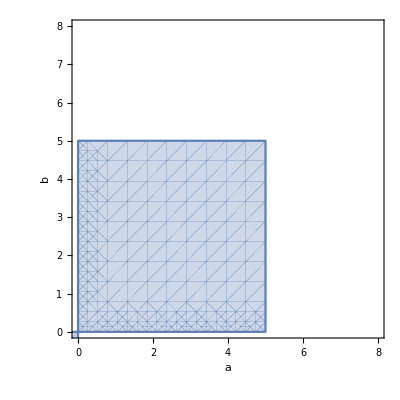

```mathematica
point={u2,v2}
jacobian2=D[f[u,v],{{u,v}}]/. {u->point[[1]],v->point[[2]]};
simplifiedJacobian2=Simplify[jacobian2];
MatrixForm[simplifiedJacobian2]
fu2=simplifiedJacobian2[[1,1]]
fv2=simplifiedJacobian2[[1,2]]
gu2=simplifiedJacobian2[[2,1]]
gv2=simplifiedJacobian2[[2,2]]
(*condition1&&2*)
RegionPlot[fu2+gv2<0&&fu2*gv2-fv2*gu2>0,{a,-5,5},{b,-5,5},FrameLabel->{"a","b"},LabelStyle->Directive[Black,Medium],PlotRange->{{0,8},{0,8}}]
```